```mathematica
Kc = 1; (*We set a constant coupling between oscillators*)
n=10;
ω = RandomReal[1,n];
Theta = Table[Subscript[θ, i],{i,1,n}];
```

```mathematica
(*creating Differential equations*)
Dlist = Table[ω[[i]]+Kc/n Sum[Sin[Theta[[j]][t]-Theta[[i]][t]],{j,1,n}],{i,1,n}];
```

```mathematica
eqs=Table[D[Theta[[i]][t],t]==Dlist[[i]],{i,1,n}];
inis = Table[Theta[[i]][0]==RandomReal[2Pi],{i,1,n}];
sol=NDSolve[{eqs,inis},Theta ,{t,0,10}];
```

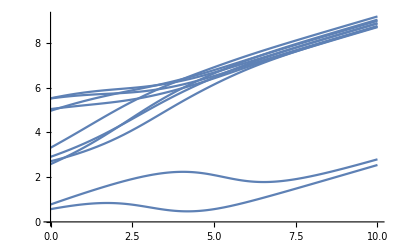

```mathematica
Plot[Table[Theta[[i]][t],{i,1,n}]/.sol,{t,0,10}]
```

```mathematica
(*Define the order parameter*)
Δ = 1/n Sum[Exp[ⅈ Theta[[i]][t]]/.sol,{i,1,n}];
```

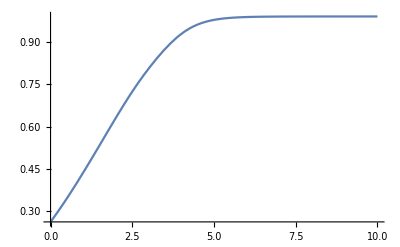

```mathematica
Plot[Norm[Δ],{t,0,10}]
```

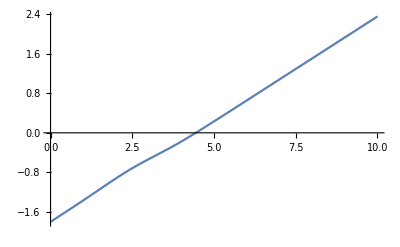

```mathematica
Plot[Arg[Δ],{t,0,10}]
```